```mathematica
sig1=Table[Sin[2 π *0.03* k],{k,1,500}];
sig2=Table[0.8*Sin[2 π *0.03* k+2π*0.15],{k,1,500}];
sig3=Table[0.95*Sin[2 π *0.03* k+2π*0.3],{k,1,500}];
sig4=Table[0.85*Sin[2 π *0.03* k+2π*0.45],{k,1,500}];
```

```mathematica
SigM = Transpose[{{sig1},{sig2},{sig3},{sig4}}];
MatrixForm[SigM];
```

```mathematica
{u,w,v}=SVD=Chop[SingularValueDecomposition[SigM]];
```

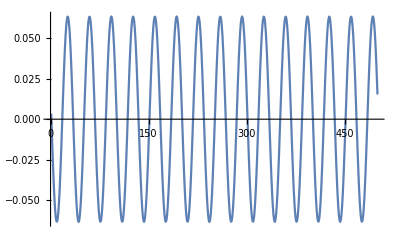

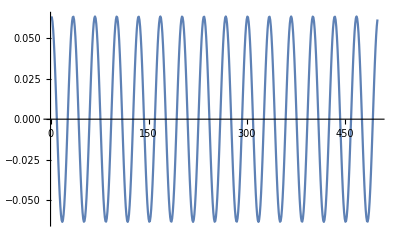

```mathematica
MatrixForm[w];
Ut1 = Transpose[v][[1]];
ListPlot[Ut1,Joined->True, PlotRange->All]
Ut2 = Transpose[v][[2]];
ListPlot[Ut2,Joined->True, PlotRange->All]
```

16

0.03

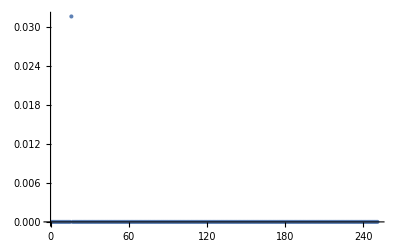

```mathematica
fsig=Fourier[Ut1,FourierParameters->{-1,1}];
fsig=Take[fsig,{1,Length[Ut1]/2+1}];
y=Abs[fsig];
maxY500=Max[y];
n=Position[y,maxY500][[1,1]]
len=Length[Ut1];
nu=Table[1.0*x/len,{x,0,len-1}];
nu500 = nu[[n]]
ListPlot[y,PlotRange->All]
```

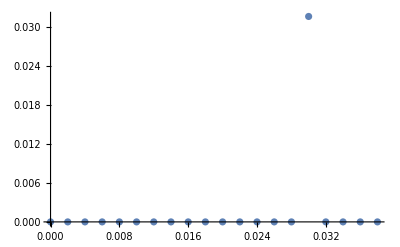

```mathematica
ListPlot[Transpose[{nu[[1;;n+4]],y[[1;;n+4]]}],PlotRange->All]
```

```mathematica
Ut2 = Transpose[SVD[[1;3]]][[2]];
ListPlot[Ut2,Joined->True, PlotRange->All]
```

-Graphics-

```mathematica
fsig=Fourier[Ut2,FourierParameters->{-1,-1}];
fsig=Take[fsig,{1,Length[Ut2]/2+1}];
y=Abs[fsig];
maxY500=Max[y];
n=Position[y,maxY500][[1,1]]
len=Length[Ut2];
nu=Table[1.0*x/len,{x,0,len-1}];
nu500 = nu[[n]]
ListPlot[y,PlotRange->All]
ListPlot[Transpose[{nu[[1;;n+4]],y[[1;;n+4]]}],PlotRange->All]
```

16

0.03

-Graphics-

-Graphics-